```mathematica
subway = Import["Downloads/1629 1st Ave 5.m4a"];
```

```mathematica
subway
```

```mathematica
t = AudioTrim[subway,{21,23}] ;
```

```mathematica
Import["https://commons.wikimedia.org/wiki/File:Ada_Jones_und_Len_Spencer,_Return_of_the_Arkansas_Traveler,_Indestructible_Record_3108,_1910.mp3", "MP3"]
```

Import::fmterr: Cannot import data as MP3 format.

$Failed

```mathematica
AudioResample[subway, .1]
```

AudioResample::srate: The sample rate should be a positive machine-sized integer number or a Quantity representing frequency instead of 0.1.

AudioResample[,0.1]

```mathematica
a=ExampleData[{"Sound","RollingCoin"},"Audio"];
AudioSampleRate[a]
```

44100 Hz

```mathematica
a
```

```mathematica
AudioJoin@@Table[t, 10]
```

```mathematica
cp = Import["Downloads/videoplayback.mp4"];
```

```mathematica
cp
```

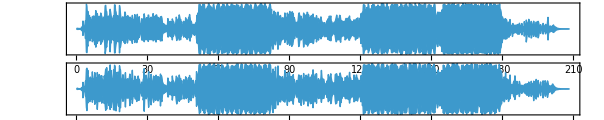

```mathematica
AudioPlot[cp]
```

```mathematica
Spectrogram[cp]
```

-Graphics-

```mathematica
AudioOverlay[{cp, subway}, SampleRate->2048]
```

```mathematica
AudioOverlay[{cp, subway}, SampleRate->2048]
```

```mathematica
AudioTrim[cp, {1, 10}]
```

```mathematica
chorus = AudioTrim[cp, {51.2, 82.5}]
```

```mathematica
steps = ;
```

```mathematica
AudioOverlay[{chorus, steps}]
```

```mathematica
chorus
```

```mathematica
mono=Import["ExampleData/rule30.wav"]
```

```mathematica
stereo=AudioChannelMix[mono,"Stereo"]
```

```mathematica
AudioChannelSeparate[chorus]
```

{,}

```mathematica
a=ExampleData[{"Audio","DogBark"},"Audio"]
```

```mathematica
AudioChannelSeparate[a]
```

{,}

```mathematica
AudioNormalize[]
```

```mathematica
AudioAmplify[, 2]
```

```mathematica
Export["Projects/Wolfram/Sound/bleedingout.mp3", chorus, "mp3"]
```

Projects/Wolfram/Sound/bleedingout.mp3